```mathematica
Off[General::partw]
Off[General::strse]
fplist={"400cfs","800cfs","1200cfs","1600cfs","3000cfs","4000cfs","5000cfs","6000cfs","10000cfs","15000cfs","20000cfs","40000cfs","50000cfs"}

Do[

rawdata=Import[StringJoin["C:\\Users\\Sam\\Desktop\\Thesis Work\\Tar Flooding Extents\\",fplist[[k]],".sdf"],"Words"];
fpath=StringJoin["C:\\Users\\Sam\\Desktop\\Thesis Work\\Tar Flooding Extents\\",fplist[[k]],".csv"];

WATERnumbers={};
ENDnumbers={};
For[i=1,i<Length[rawdata],i++,
If[rawdata[[i]]=="WATER",WATERnumbers=Append[WATERnumbers,i]];
If[rawdata[[i]]=="CROSS-SECTION:",ENDnumbers=Append[ENDnumbers,i-1]];
];
ENDnumbers=Delete[ENDnumbers,1];

elevations={};
extents={};
For[i=1,i<Length[WATERnumbers],i=i+2,
el=rawdata[[WATERnumbers[[i]]+1]];
elevations=Append[elevations,el];
ex1=WATERnumbers[[i+1]]+3;
ex2=WATERnumbers[[i+1]]+6;
extents=Append[extents,rawdata[[ex1;;ex2]]];
];

For[i=1,i<Length[extents]+2,i++,
For[j=1,j<4,j++,
extents[[i,j]]=StringReplace[extents[[i,j]],","->""];
];
];
For[i=1,i<Length[elevations]+2,i++,
elevations[[i]]=StringReplace[elevations[[i]],"ELEVATION:"->""];
];

x=Table[{Transpose[ToExpression[extents]][[1]],Transpose[ToExpression[extents]][[3]]}]//Flatten;
y=Table[{Transpose[ToExpression[extents]][[2]],Transpose[ToExpression[extents]][[4]]}]//Flatten;
z=Flatten[Table[{elevations,elevations}//Transpose//ToExpression]];

exlist=Table[{x[[i]],y[[i]],z[[i]],fplist[[k]]},{i,1,Length[x]}];
Export[fpath,exlist,"CSV"]


,{k,1,Length[fplist]}]
On[General::partw]
On[General::strse]
```

{400cfs,800cfs,1200cfs,1600cfs,3000cfs,4000cfs,5000cfs,6000cfs,10000cfs,15000cfs,20000cfs,40000cfs,50000cfs}

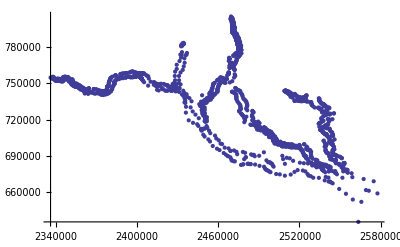

```mathematica
ListPlot[Transpose[Table[{x,y}]]]
```

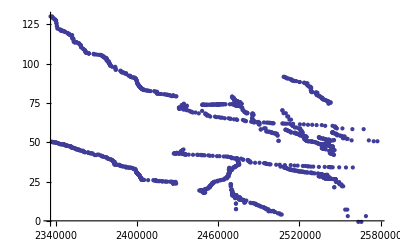

```mathematica
ListPlot[Transpose[Table[{x,z}]]]
```